# Hydrogen Atom

## (Visualization atomic orbital)

## Plotting atomic orbitals

```mathematica
(*Angular part*)
Θ [θ_,ϕ_,l_,m_]:= SphericalHarmonicY[l,m,θ,ϕ]
(*Radial part*)
R[r_,n_,l_] := Sqrt[(2/n)^3((n-l-1)!)/(2n*(n+l)!)]Exp[-r/n]((2r)/n)^l LaguerreL[n-l-1,2l+1,(2r)/n] (*Setting Bohr radius to 1 (a=1)*)
(*Complete wavefunction*)
ψ [{r_,θ_,ϕ_},{n_,l_,m_}]:=R[r,n,l]Θ [θ,ϕ,l,m]
```

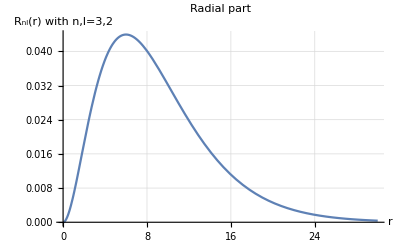

```mathematica
n=3;l=2;m=1; (*Provide principal, azimuthal and magnetic quantum numbers*)
(* Plotting Angular Part*)
GraphicsRow[{SphericalPlot3D[Abs[Θ[θ,ϕ,l,m]],{θ,0,Pi},{ϕ,0,2Pi},PlotLabel->Style["Angular part",FontSize->26]],
(*Plotting Radial Part*)
Plot[R[r,n,l],{r,0,30},GridLines->Automatic,AxesLabel->{"r",StringForm["R_nl(r) with n,l=``,``",n,l ]},PlotLabel->Style["Radial part",FontSize->26]],
(*Plotting probability density |ψ|^2*)
DensityPlot3D[Abs[ψ[{Sqrt[x^2+y^2+z^2],ArcTan[z,Sqrt[x^2+y^2]],ArcTan[x,y]},{n,l,m}]]^2,{x,-30,30},{y,-30,30},{z,-30,30},AxesLabel->{"x","y","z"},PlotLabel->Style["|ψ|^2",FontSize->26],PlotLegends->Automatic,ImageSize->Medium]},ImageSize->Full]
```